# NanoREST Clustering

Nano Startuppaclet:NanoREST/tutorial/Clustering#604775092 | Analyticspaclet:NanoREST/tutorial/Clustering#1808925427
Clusteringpaclet:NanoREST/tutorial/Clustering#1035121784 | Pattern Generationpaclet:NanoREST/tutorial/Clustering#1313035530

Demonstration on using the Mathematica API of the Boon Nano

Load the package

```mathematica
<<NanoREST`
```

## Nano Startup

OpenNano[Label] | starts a new nano instance with the given label
CloseNano[NanoHandle] | frees the running nano
NanoList[NanoHandle] | returns a list of running nano instances

Nano Instances.

Call this function to start a nano instance

```mathematica
nano=OpenNano["test"]
```

<|api-key→no-key,api-tenant→no-tenant,url→http://localhost:5007/expert/v3/,instance→test|>

Now the nano, "test",  has been initialized and the association returned will be used later in the clustering calls in order to know which nano instance the cluster calls should talk to. Calling CloseNanopaclet:NanoREST/ref/CloseNano[nano] frees up the nano instance, but it is not recoverable unless it is saved first .

Next, configuring the nano sets up the correct number of features (or columns of data) using the specified data types along with setting initial minimum values, maximum values, weights for the columns, percent variation, accuracy, and streaming window. These can be autotuned later but must first be initialized before adding data or running the nano.

GetConfig[InstanceID] | returns the cluster parameters values
ConfigureNano[NumericaFormat, FeautreCount, Min, Max, PercentVariation, StreamingWindow, Weight, Accuracy] | posts the parameters for reading and clustering data
AutotuneConfig[InstanceID] | returns an unsupervised selection of min, max and percent variation values
SaveNano[InstanceID,filename] | gets the nano state for the InstanceID to save for later use

Initializing cluster parameters.

Post the clustering parameters

```mathematica
ConfigureNano[nano,float32,20,0,2,0.05]
```

With the config initialized, the data can be uploaded and clustered. The nano will return a 400 error code if the data is posted before the config because it needs to know how how many features to read in and what data type. The initial config doesn't need to be the final values since you can change them later or autotune, but the number of features needs to be accurate for the data to be read in correctly.

### Parameters breakdown

The nano has three options for types of data: float, int, and native. Float data is just that, int data is any integer data, and native data is integer data that has a minimum value of 0. All three versions talk to each other and run the same way in the background but the specification is necessary to save that little bit of time when running native data so that the background conversion step is skipped. In other words, running a float or int run converts the data to native and works with it in that form then converts it back so native data is naturally faster.

The number of features (or pattern length) along with the minimum and maximum values are used in the nano to calculate the percent variation. The percent variation is a distance statistic specific to the nano that determines how different two vectors are from each other.

Percent variation is a kind of Manhattan distance where the distance is measured component-wise between the two waveforms, and then normalized to be a value between 0 and 1 where 0 is the same waveform and 1 is completely opposite waveforms. Each waveform that is measured could also be thought of as a point in n-dimensional space where n is the pattern length of the waveform. For a simple example, take the waveforms A={1,4,5} and B={3,0,2}. These can be thought of as 3-dimensional points or 2-dimensional waveforms

Example points in 3D space

```mathematica
ListPointPlot3D[{{Labeled[{1,4,5},"A"]},{Labeled[{3,0,2},"B"]}},PlotStyle->{{PointSize[.05]}},BoxRatios->{1, 1, 1},PlotRange->{{-1,6},{-1,6},{-1,6}}]
```

-Graphics3D-

Example points in 2D

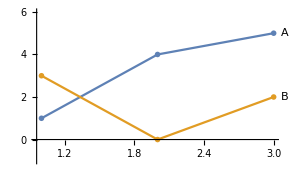

```mathematica
ListLinePlot[{Labeled[{1,4,5},"A"],Labeled[{3,0,2},"B"]},PlotRange->{All,{-1,6}},PlotMarkers->{●,●}]
```

Visualizing the waveforms in n-dimensional space is a better representation of a Euclidean distance measurement but when thinking of percent variation, the 2D visualization is more accurate in how it is measured. Percent variation takes the absolute value of the differences of each column, and takes the total sum of those values divided by the box area.

The box area is the range of the min and max values multiplied by the pattern length. In this example, if the min is -1 and the max is 6, the box area would be 21. The column differences would be 2, 4, and 3 respectively for a final percent variation of 9/21 = 3/7 = 0.428.

When using the nano, instead of specifying the number of clusters, the percent variation is set to determine how close together the waveforms must be to be in the same cluster. This can be set manually or autotuned to the dataset (described in the autotuning section).

The weights are 0 and 1 values that specify which columns should be used when clustering. This is kind of a manual PCA step where instead of altering the data and removing columns, the weights can just be set to zero and those columns will just be ignored when calculating the percent variation.

In running the nano, there is also a variable of accuracy for statistical significance. The nano uses statistical models so when setting a higher accuracy, it takes a little longer to run but the clustering is more reliable. The default value is 0.99, since the run time is still fast enough, but this can be set fairly low (such as 0.8) and still get decent results from the nano. It is not a very sensitive value in regards to nano results.

The final parameter is the streaming window size. This value, in the most simple case, is for single sensor time-series data. When receiving a single stream of values, the nano can take a set number of those values and cluster as one waveform, then shift over one and take the next window of values to cluster and so on and so forth.

Streaming window size of 25

```mathematica
Manipulate[Show[ListLinePlot[{Take[NanoREST`r,100],Transpose[{Table[i+j,{j,0,25-1}],Take[NanoREST`r,{i,i+25-1}]}]},PlotRange->All,PlotMarkers->{Automatic, 10}],Graphics[{EdgeForm[{Thick}],FaceForm[],Rectangle[{i,0},{i+25-1,1.39}]}]],{i,1,Length[NanoREST`r]-25+1,1}]
```

The streaming window is defaulted to 1 since most of the nano clustering is done on vectors, but the streaming window can still be set to a higher value in those cases. An application is when dealing with position mapping, if the data is a list of (x, y) positions in time, a streaming window of 10 would take the first ten positions and concatenate the (x, y) values into a vector of length 20 and cluster the new waveform.

### Autotuning

Once the parameters are initialized, the data can be uploaded and clustered. In order to make the nano as unsupervised as possible, Autotunepaclet:NanoREST/ref/Autotune[InstanceID] can be run on the dataset to find the optimal minimum and maximum values as well as the percent variation.

Create artificial data

```mathematica
data=Flatten[Table[GenerateRandomVariantFloat[GenerateRandomPatternFloat[20,0,2],0,2,0.01,RandomInteger[{1,10}],1,Exact->False],5],1];
```

Post data to autotune

```mathematica
LoadData[nano,data]
```

```mathematica
AutotuneConfig[nano]
```

```mathematica
GetConfig[nano]["percentVariation"]
```

0.032

The min and max values are set based on the .5 and 99.5 percentiles of the dataset, and any data that falls outside this range is just rounded down (or up).

The percent variation is a little trickier. Setting this value is like setting k in a k-means clustering algorithm and is a difficult thing to automate since each case is vastly different and could have multiple "correct" answers.

Most approaches to automate the number of clusters in k-means try and cluster with various different k's and run a simple test on which works the best for the data. There are multiple issues with this. The main is that k-means is so slow that the clustering cannot be done on all the different values of k or even all k's in a range. This means the test on which k is best is incomplete.

The nano, however, is fast enough that the autotuning approach runs the clustering using percent variation values between 1% and 20% and tests with those results. Doing the equivalent with k-means would mean that in some cases, there would be over 10,000 clusters and that would take hours, but with the nano, it takes seconds.

The autotuning uses the total number of clusters that were created for each percent variation and finds the "elbow". This is essentially where percent variations to the left give exponentially more clusters for each iteration over because decreasing the percent variation just splits up the natural clusters into smaller and smaller pieces. Percent variation values to the right don't change the number of clusters as much. The main clusters have been separated and changing the percent variation alters a few middle vectors but for the most part, the clustering stays the same.

Clustering visualization using euclidean distance clustering

```mathematica
Manipulate[Module[{index=LengthWhile[NanoREST`c,Transpose[#]⟦3,1⟧≥dist&]},GraphicsRow[{Show[ListPlot[NanoREST`points,PlotRange->{{0,4},{0,4}},PlotStyle->PointSize[0.01],AspectRatio->1],Graphics[Table[Circle[NanoREST`c⟦index,i,{1,2}⟧,NanoREST`c⟦index,i,3⟧],{i,1,Length[NanoREST`c⟦index⟧]}]]],ListLinePlot[Transpose[{{2,1.5,1,.75,.5,.25},Length/@NanoREST`c}],PlotRange->All,PlotMarkers->Automatic]},ImageSize->Medium]],{dist,{.25,.5,.75,1,1.5}},ContinuousAction->False]
```

In this example, using a euclidean distance of around 0.5 would be the autotuned value of this clustering technique.

For a similar idea yet more rudimentary approach: see this article.https://www.datasciencecentral.com/profiles/blogs/how-to-automatically-determine-the-number-of-clusters-in-your-dat

## Clustering

At this point, the parameters are set and the data is uploaded so all that's left is to run the nano. This is done with RunNanopaclet:NanoREST/ref/RunNano[NanoHandle]. Calling that alone would run the nano and return a success or fail code. Then calling any of the get cluster statistics would return the analytics from that nanorun.

LoadData[NanoHandle] | uploads the data to be clustered and returns any results specified (if any)
RunNano[NanoHandle] | runs the nano on the posted data
runs the nano and returns the specified cluster analytics

Nano run options.

Post the nano run and optionally print the analytics directly (in the nano run or when posting data)

```mathematica
RunNano[nano,Results->ID]
```

<|ID→{1,1,1,1,2,2,2,2,2,2,2,2,2,3,3,3,3,3,4,4,4,4,5,5,5,5,5,5,5,5}|>

```mathematica
LoadData[nano,data,AppendData->False]
RunNano[nano,Results->All]
```

<|DI→{311,311,311,311,433,433,433,433,433,433,433,433,433,346,346,346,346,346,293,293,293,293,404,404,404,404,404,404,404,404},FI→{2012,2012,2012,2012,1255,1255,1255,1255,1255,1255,1255,1255,1255,1000,1000,1000,1000,1000,903,903,903,903,1204,1204,1204,1204,1204,1204,1204,1204},ID→{1,1,1,1,2,2,2,2,2,2,2,2,2,3,3,3,3,3,4,4,4,4,5,5,5,5,5,5,5,5},RI→{0,0,0,0,377,377,377,377,377,377,377,377,377,504,504,504,504,504,552,552,552,552,402,402,402,402,402,402,402,402},SI→{155,155,153,151,147,138,122,89,22,46,93,188,377,377,377,378,380,384,392,408,441,505,506,509,513,523,542,533,514,477}|>

```mathematica
RunNano[nano,Results->All]
```

<|DI→{311,311,311,311,433,433,433,433,433,433,433,433,433,346,346,346,346,346,293,293,293,293,404,404,404,404,404,404,404,404},FI→{1725,1725,1725,1725,1217,1217,1217,1217,1217,1217,1217,1217,1217,1000,1000,1000,1000,1000,917,917,917,917,1173,1173,1173,1173,1173,1173,1173,1173},ID→{1,1,1,1,2,2,2,2,2,2,2,2,2,3,3,3,3,3,4,4,4,4,5,5,5,5,5,5,5,5},RI→{0,0,0,0,295,295,295,295,295,295,295,295,295,421,421,421,421,421,469,469,469,469,320,320,320,320,320,320,320,320},SI→{401,399,396,390,378,354,306,210,17,36,73,147,295,295,295,296,298,302,310,326,358,422,423,426,430,440,459,450,431,394}|>

Running two consecutive nano runs will just re-cluster the previous data. Additionally, when posting the data, setting AppendData->True will concatenate the new data set with the previously posted data. This is useful if you want to re-cluster previous data and also cluster the new data. Also appending the data is helpful when the previous data has not yet been clustered.

### Saving or restoring a nano run

When opening a nano, a previous version can be loaded at that time as well using the "Filename" option in OpenNanopaclet:NanoREST/ref/OpenNano. SaveNanopaclet:NanoREST/ref/SaveNano[NanoHandle, Filename] saves the current nano run so it can used again later. If no filename is supplied to SaveNanopaclet:NanoREST/ref/SaveNano, the default is to save a file named "Untitled-index.bn".

Save version

```mathematica
snapshotFile=SaveNano[nano]
```

Untitled-1.bn

Delete current instance

```mathematica
CloseNano[nano]
```

Reloading the snapshot sets the config with the previous values

```mathematica
nano=OpenNano["test","default","Filename"->snapshotFile];
```

```mathematica
GetConfig[nano]
```

<|accuracy→0.99,features→{<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>,<|maxVal→1.97295,minVal→0.00145137,weight→1|>},numericFormat→float32,percentVariation→0.032,streamingWindowSize→1|>

## Analytics

GetBufferStatus[InstanceID] | gives the byte information on the buffer
GetNanoResults[InstanceID] | returns the list of results corresponding to each pattern
GetNanoStatus[InstanceID] | gives the results relating to each cluster

Cluster analytics.

Post data and run clustering

```mathematica
LoadData[nano,data]
```

```mathematica
RunNano[nano]
```

Get analytics

```mathematica
GetBufferStatus[nano]
```

<|totalBytesInBuffer→2400,totalBytesProcessed→2400,totalBytesWritten→2400|>

```mathematica
GetNanoResults[nano]
```

<|DI→{311,311,311,311,433,433,433,433,433,433,433,433,433,346,346,346,346,346,293,293,293,293,404,404,404,404,404,404,404,404},FI→{1572,1572,1572,1572,1196,1196,1196,1196,1196,1196,1196,1196,1196,1000,1000,1000,1000,1000,925,925,925,925,1157,1157,1157,1157,1157,1157,1157,1157},ID→{1,1,1,1,2,2,2,2,2,2,2,2,2,3,3,3,3,3,4,4,4,4,5,5,5,5,5,5,5,5},RI→{0,0,0,0,240,240,240,240,240,240,240,240,240,364,364,364,364,364,412,412,412,412,265,265,265,265,265,265,265,265},SI→{0,0,0,0,0,1,3,7,14,29,59,119,240,240,240,241,243,247,255,271,302,365,366,369,373,383,403,393,375,338}|>

```mathematica
GetNanoStatus[nano]
```

<|PCA→{{0,0,0},{0.294,0.381,0.431},{0,1,0.309},{0.272,0.309,1},{0.463,0.294,0.371},{1,0,0.272}},anomalyIndexes→{1000,0,240,364,412,265},clusterGrowth→{0,1,5,14,19,23},clusterSizes→{0,111,36,20,16,32},distanceIndexes→{0,311,433,346,293,404},frequencyIndexes→{0,1572,1196,1000,925,1157},numClusters→6,totalInferences→120|>

### PCA

The PCA function is a visual representation way to represent the spatial distribution of the clusters. This uses the pattern memory and transforms it to three dimensions. The first three values in each coordinate returned is the projection of the pattern memory from the pattern memory space to the reduced dimension space. These can be used to plot the pattern memory in 3D or using RGB values to get a visual result in how different the clusters are. The forth coordinate is the raw frequency index. Another visual representation is by using the first two projections and the frequency index as the third coordinate to get a representation of the clustering with both the spatial and frequency aspects represented.

Plot 3D projections with RGB coloring

```mathematica
p=GetNanoStatus[nano,Results->PCA]["PCA"];
```

```mathematica
ListPointPlot3D[{#}&/@p,PlotRange->All,BoxRatios->{1, 1, 1},PlotStyle->Table[{PointSize[0.05],RGBColor[p⟦i⟧]},{i,1,Length[p]}]]
```

-Graphics3D-

## Pattern Generation

Generating patterns is used for testing purposes when artificial data is needed with a set number of clusters or a set distance apart. The following functions generate random vectors for the given specifications.

GenerateRandomPatternNative[PatternLength,MaxVal]
GenerateRandomPatternNative[MaxVals] | creates a random vector of integer values from 0 to MaxVal(s)
GenerateRandomPatternInt[PatternLength,MinVal,MaxVal]
GenerateRandomPatternInt[MinVals,MaxVals] | creates a random vector of integer values from MinVals(s) to MaxVal(s)
GenerateRandomPatternFloat[PatternLength,MinVal,MaxVal]
GenerateRandomPatternFloat[MinVals,MaxVals] | creates a random vector of float values from MinVal(s) to MaxVal(s)
GenerateRandomVariantNative[SourcePattern, MaxVal, PercentVariation, Num,WeightsIn] | generates Num pseudo random integer vector(s) with values from 0 to MaxVal using the columns that correspond to WeightsIn of 1 (or all columns when WeightsIn == 0) that deviates from SourcePattern by at most PercentVariation when Exact->False
GenerateRandomVariantInt[SourcePattern, MinVal, MaxVal, PercentVariation, Num,Weights] | generates Num pseudo random integer vector(s) with values from MinVal to MaxVal using the columns that correspond to WeightsIn of 1 (or all columns when WeightsIn == 0) that deviates from SourcePattern by at most PercentVariation when Exact->False
GenerateRandomVariantFloat[SourcePattern, MinVal, MaxVal, PercentVariation, Num,Weights] | generates Num pseudo random float vector(s) with values from MinVal to MaxVal using the columns that correspond to WeightsIn of 1 (or all columns when WeightsIn == 0) that deviates from SourcePattern by at most PercentVariation when Exact->False

Creating random pattern vectors.

ComputePercentVariation[v_1, v_2, MinVal, MaxVal] | calculates the percent variation between v_1 and v_2 using the MinVal and MaxVal (along with the length of the vectors) as the box area

Percent Variation.

Calculating the percent variation is yet another test for the data. This is as simple as just comparing two waveforms to see if they were correctly clustered or some other test.

Generate random vectors with vectors 5% away from each

```mathematica
patterns=Flatten[Table[GenerateRandomVariantInt[GenerateRandomPatternInt[25, -10, 10],-10,10,0.05,10],2],1];
```

```mathematica
TableForm[Table[ComputePercentVariation[patterns⟦i⟧,patterns⟦j⟧,-10,10],{i,1,Length[patterns]},{j,1,Length[patterns]}]]
```

0. | 0.0457143 | 0.0380952 | 0.0495238 | 0.0304762 | 0.04 | 0.0533333 | 0.0438095 | 0.0571429 | 0.047619 | 0.306667 | 0.300952 | 0.289524 | 0.32 | 0.300952 | 0.297143 | 0.300952 | 0.28381 | 0.318095 | 0.312381
0.0457143 | 0. | 0.0495238 | 0.0419048 | 0.0380952 | 0.032381 | 0.0380952 | 0.047619 | 0.0190476 | 0.0552381 | 0.302857 | 0.297143 | 0.278095 | 0.31619 | 0.289524 | 0.293333 | 0.297143 | 0.272381 | 0.314286 | 0.300952
0.0380952 | 0.0495238 | 0. | 0.0457143 | 0.0495238 | 0.0514286 | 0.0380952 | 0.0438095 | 0.0609524 | 0.0514286 | 0.306667 | 0.300952 | 0.281905 | 0.32 | 0.293333 | 0.297143 | 0.300952 | 0.27619 | 0.318095 | 0.304762
0.0495238 | 0.0419048 | 0.0457143 | 0. | 0.0495238 | 0.0361905 | 0.0342857 | 0.0590476 | 0.0304762 | 0.0438095 | 0.306667 | 0.304762 | 0.278095 | 0.31619 | 0.300952 | 0.297143 | 0.308571 | 0.28381 | 0.314286 | 0.308571
0.0304762 | 0.0380952 | 0.0495238 | 0.0495238 | 0. | 0.0361905 | 0.0533333 | 0.0361905 | 0.0419048 | 0.0552381 | 0.299048 | 0.300952 | 0.281905 | 0.312381 | 0.300952 | 0.289524 | 0.300952 | 0.28381 | 0.310476 | 0.312381
0.04 | 0.032381 | 0.0514286 | 0.0361905 | 0.0361905 | 0. | 0.0552381 | 0.0342857 | 0.0285714 | 0.0533333 | 0.31619 | 0.306667 | 0.295238 | 0.325714 | 0.310476 | 0.306667 | 0.310476 | 0.293333 | 0.32381 | 0.318095
0.0533333 | 0.0380952 | 0.0380952 | 0.0342857 | 0.0533333 | 0.0552381 | 0. | 0.0590476 | 0.0266667 | 0.047619 | 0.306667 | 0.304762 | 0.278095 | 0.31619 | 0.300952 | 0.297143 | 0.308571 | 0.28381 | 0.314286 | 0.308571
0.0438095 | 0.047619 | 0.0438095 | 0.0590476 | 0.0361905 | 0.0342857 | 0.0590476 | 0. | 0.0514286 | 0.0533333 | 0.308571 | 0.302857 | 0.291429 | 0.321905 | 0.302857 | 0.299048 | 0.302857 | 0.285714 | 0.32 | 0.314286
0.0571429 | 0.0190476 | 0.0609524 | 0.0304762 | 0.0419048 | 0.0285714 | 0.0266667 | 0.0514286 | 0. | 0.0438095 | 0.306667 | 0.304762 | 0.278095 | 0.31619 | 0.300952 | 0.297143 | 0.308571 | 0.28381 | 0.314286 | 0.308571
0.047619 | 0.0552381 | 0.0514286 | 0.0438095 | 0.0552381 | 0.0533333 | 0.047619 | 0.0533333 | 0.0438095 | 0. | 0.312381 | 0.310476 | 0.28381 | 0.321905 | 0.306667 | 0.302857 | 0.314286 | 0.289524 | 0.32 | 0.314286
0.306667 | 0.302857 | 0.306667 | 0.306667 | 0.299048 | 0.31619 | 0.306667 | 0.308571 | 0.306667 | 0.312381 | 0. | 0.0590476 | 0.04 | 0.032381 | 0.047619 | 0.0361905 | 0.0285714 | 0.0609524 | 0.0304762 | 0.047619
0.300952 | 0.297143 | 0.300952 | 0.304762 | 0.300952 | 0.306667 | 0.304762 | 0.302857 | 0.304762 | 0.310476 | 0.0590476 | 0. | 0.0495238 | 0.0571429 | 0.0457143 | 0.0457143 | 0.0495238 | 0.0361905 | 0.0438095 | 0.0419048
0.289524 | 0.278095 | 0.281905 | 0.278095 | 0.281905 | 0.295238 | 0.278095 | 0.291429 | 0.278095 | 0.28381 | 0.04 | 0.0495238 | 0. | 0.0457143 | 0.0495238 | 0.0266667 | 0.0609524 | 0.047619 | 0.0628571 | 0.0533333
0.32 | 0.31619 | 0.32 | 0.31619 | 0.312381 | 0.325714 | 0.31619 | 0.321905 | 0.31619 | 0.321905 | 0.032381 | 0.0571429 | 0.0457143 | 0. | 0.0495238 | 0.0495238 | 0.0457143 | 0.0628571 | 0.032381 | 0.0533333
0.300952 | 0.289524 | 0.293333 | 0.300952 | 0.300952 | 0.310476 | 0.300952 | 0.302857 | 0.300952 | 0.306667 | 0.047619 | 0.0457143 | 0.0495238 | 0.0495238 | 0. | 0.0533333 | 0.0380952 | 0.032381 | 0.047619 | 0.0571429
0.297143 | 0.293333 | 0.297143 | 0.297143 | 0.289524 | 0.306667 | 0.297143 | 0.299048 | 0.297143 | 0.302857 | 0.0361905 | 0.0457143 | 0.0266667 | 0.0495238 | 0.0533333 | 0. | 0.0495238 | 0.0438095 | 0.0590476 | 0.0571429
0.300952 | 0.297143 | 0.300952 | 0.308571 | 0.300952 | 0.310476 | 0.308571 | 0.302857 | 0.308571 | 0.314286 | 0.0285714 | 0.0495238 | 0.0609524 | 0.0457143 | 0.0380952 | 0.0495238 | 0. | 0.0514286 | 0.0285714 | 0.0533333
0.28381 | 0.272381 | 0.27619 | 0.28381 | 0.28381 | 0.293333 | 0.28381 | 0.285714 | 0.28381 | 0.289524 | 0.0609524 | 0.0361905 | 0.047619 | 0.0628571 | 0.032381 | 0.0438095 | 0.0514286 | 0. | 0.0533333 | 0.04
0.318095 | 0.314286 | 0.318095 | 0.314286 | 0.310476 | 0.32381 | 0.314286 | 0.32 | 0.314286 | 0.32 | 0.0304762 | 0.0438095 | 0.0628571 | 0.032381 | 0.047619 | 0.0590476 | 0.0285714 | 0.0533333 | 0. | 0.047619
0.312381 | 0.300952 | 0.304762 | 0.308571 | 0.312381 | 0.318095 | 0.308571 | 0.314286 | 0.308571 | 0.314286 | 0.047619 | 0.0419048 | 0.0533333 | 0.0533333 | 0.0571429 | 0.0571429 | 0.0533333 | 0.04 | 0.047619 | 0.

So in this example, the there are two clusters where the first 10 vectors are each within 5% from each other then are quite different from vectors in the other cluster.

Finish up working with the nano by clearing the instances if you are completely done with them (since they are not recoverable without saving the nanoState)

Close the nano

```mathematica
CloseNano[nano]
```

Related Guides

NanoREST